This notebook is a supplementary realization/simulation of the 1D example provided in the IROS Paper Mapping, “Foraging, and Coverage with a Particle Swarm Controlled by Uniform Inputs” to be published in IROS 2017. More specifically, it addresses the optimality and competitive factor of the bicriteria problem addressed in Section III.A.3. 

For a primer we are assuming that the particle starts from the left side at a random distance of d and moves unit distances every step. The particle will move the minimum number of steps to completely map out the 1D line and scan according to the rule “perform the ith scan at each

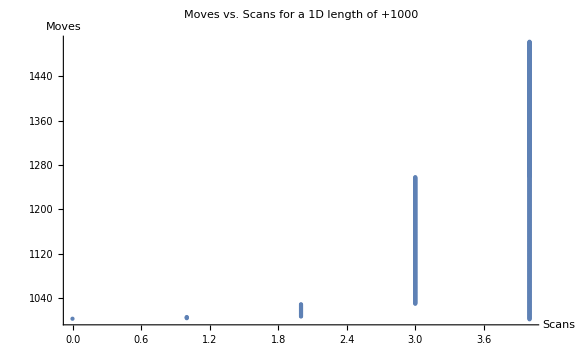

```mathematica
trials=1000;
move=0; scan=1;l=1000;
d=RandomInteger[{0,l}];
(*NumberLinePlot[{d, Interval[{0,l}]},ImageSize->Large];
moves=Min[{2d+(l-d),2(l-d)+d}]+2
scans=1;
While[scans^scans<moves,scans=scans+1];
Exponentials=Array[i^i,100];
scans=scans-1
Proof of concept for the first trial*)
Moves[x_]:=Min[{2x+(l-x),2(l-x)+x}+2];
Scans[x_]:=(temp=1;While[temp^temp<x,temp=temp+1]; temp-1)
Table[{Scans[x],Moves[x]},{x,0,l,1}];
ListPlot[Table[{Scans[x],Moves[x]},{x,1,trials,1}],PlotLabel->"Moves vs. Scans for a 1D length of "+l,AxesLabel->{Scans,Moves},ImageSize->Large]
(*Instructions on usage; change trials to change the number trials run*)
(*Text["1D Scanning and Mapping"]
Plot[Log{x,x},{x,0, 2d}]*)
(*
moves=RandomVariate[NormalDistribution[d/2,1],20];
scans=RandomVariate[NormalDistribution[d/2,1],20];
(*ListPlot[moves,PlotLabel->"Moves"]
ListPlot[scans, PlotLabel->"Scans"]*)

MRICost[n_]:=Accumulate[Prepend[RandomVariate[NormalDistribution[d/2,d/10],n]+RandomVariate[NormalDistribution[d/2,d/10],n], 0]]
ListLinePlot[Table[MRICost[6],{100}]]

HyperExponential[x_]:=x^(x+RandomVariate[NormalDistribution[d,d/10]])
Plot[HyperExponential[x],{x, 1, 3},AxesLabel->"Moves", AxesLabel->"Scans"]
Note that there are so many points that the points are jumbled to a bar graph
*)
```

For a better presentation, we are going to use the linear combination of the scans and moves as a cost function. However, we are going to have different weights.
This is represented by the  c*scan=move; The cost of a scan is a constant multiplier with respect to the cost of the move. The total cost is the sum of these costs.

```mathematica
ClearAll["Global`*"];
c=1;
Moves[m_]:=(3m+1)/2;
Scans[x_,c_]:=c*(temp=1;While[temp^temp<x,temp=temp+1]; temp-1);
(*Cost_Scans[x_]:=c*Scans[x]*)
Manipulate[LogPlot[{Moves[x]+Scans[x,1],Moves[x]+Scans[x,1000],Moves[x]+Scans[x,1000000],Moves[x]+Scans[x,1/1000]},{x,1,workspace},PlotLabel->"Cost vs. Workspace Size on a logarithmic plot", AxesLabel->{"Workspace Size","Log(Cost)"},PlotLegends->{"c=1","c=1000","c=1000000","c=1/1000"},ImageSize->Large],{workspace,5,10^8}
]
```